1.05457×10^-34

SparseArray[…]

(-1.5 | 0 | 0 | 0 | 0 | 0
0 | -1.5 | 0 | 0 | 0 | 0
0 | 0 | -1.5 | 0 | 0 | 0
0 | 0 | 0 | -1.5 | 0 | 0
0 | 0 | 0 | 0 | -1.5 | 0
0 | 0 | 0 | 0 | 0 | -1.5)

The function is real-valued.

General::prng: 选项值 PlotRange -> {{x,-0.9984,1.0015},{-0.05,1.1}} 不是 All、Full、Automatic、一个机器精度正数，或者由范围指定组成的恰当列表.

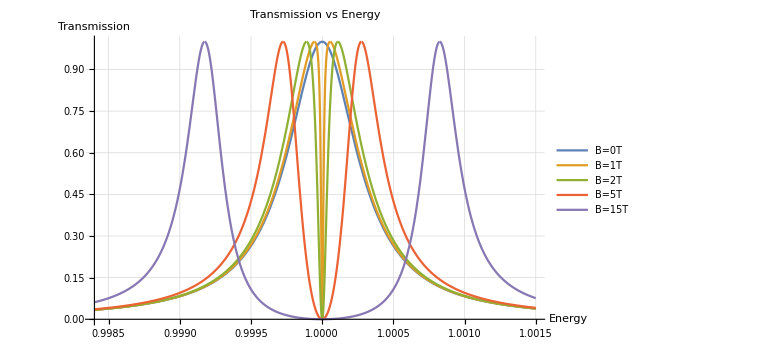

0.000471131

NIntegrate::precw: 参数函数的精度 (0.+(8.1×10^-7 ((-125.+0. ⅈ)+(93.75+0. ⅈ) x+(31.25+0. ⅈ) x^2) ((-125.+0. ⅈ)+(93.75+0. ⅈ) Conjugate[x]+(31.25+0. ⅈ) Conjugate[x]^2))/(((-364.+0.0891 ⅈ)+(594.-0.023625 ⅈ) x-(78.75+0.070875 ⅈ) x^2-(157.5+0.00225 ⅈ) x^3-(3.75-0.00675 ⅈ) x^4+(9.+0.0009 ⅈ) x^5+x^6) ((-364.-0.0891 ⅈ)+(594.+0.023625 ⅈ) Conjugate[x]-(78.75-0.070875 ⅈ) Conjugate[x]^2-(«1») «1»-(«19»+«21» ⅈ) («1»)^4+(9.-0.0009 ⅈ) Conjugate[x]^5+Conjugate[x]^6))) 小于 WorkingPrecision (20.).

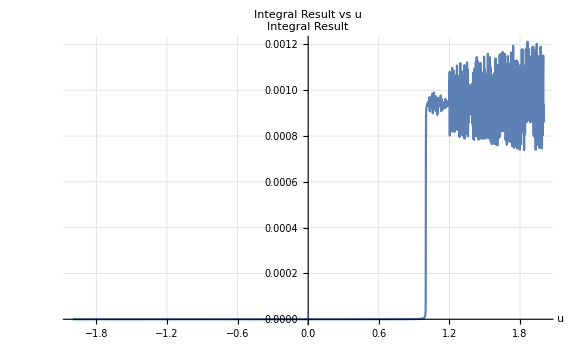

NIntegrate::inumr: 在以 {{0,2}} 为界的区域内，对于所有采样点，计算被积函数 2.41799×10^14 (0.+(8.1×10^-7 ((-37.5+0. ⅈ)+(3.125+0. ⅈ) x+(28.125+0. ⅈ) x^2+(6.25+0. ⅈ) x^3) ((-37.5+0. ⅈ)+(3.125+0. ⅈ) Conjugate[x]+(28.125+0. ⅈ) Conjugate[x]^2+(6.25+0. ⅈ) Conjugate[x]^3))/(((-364.+0.0891 ⅈ)+(594.-0.023625 ⅈ) x-(78.75+0.070875 ⅈ) x^2-(157.5+0.00225 ⅈ) x^3-(3.75-0.00675 ⅈ) x^4+(9.+0.0009 ⅈ) x^5+x^6) ((-364.-0.0891 ⅈ)+(594.+0.023625 ⅈ) Conjugate[x]-(78.75-0.070875 ⅈ) Conjugate[«1»]^2-(«1») «1»-(3.75+«21» ⅈ) («9»«1»«1»])^4+(9.-0.0009 ⅈ) Conjugate[«1»]^5+Conjugate[x]^6))) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0,2}} 为界的区域内，对于所有采样点，计算被积函数 2.41799×10^14 (0.+(8.1×10^-7 ((-37.5+0. ⅈ)+(3.125+0. ⅈ) x+(28.125+0. ⅈ) x^2+(6.25+0. ⅈ) x^3) ((-37.5+0. ⅈ)+(3.125+0. ⅈ) Conjugate[x]+(28.125+0. ⅈ) Conjugate[x]^2+(6.25+0. ⅈ) Conjugate[x]^3))/(((-364.+0.0891 ⅈ)+(594.-0.023625 ⅈ) x-(78.75+0.070875 ⅈ) x^2-(157.5+0.00225 ⅈ) x^3-(3.75-0.00675 ⅈ) x^4+(9.+0.0009 ⅈ) x^5+x^6) ((-364.-0.0891 ⅈ)+(594.+0.023625 ⅈ) Conjugate[x]-(78.75-0.070875 ⅈ) Conjugate[«1»]^2-(«1») «1»-(3.75+«21» ⅈ) («9»«1»«1»])^4+(9.-0.0009 ⅈ) Conjugate[«1»]^5+Conjugate[x]^6))) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

$Aborted

```mathematica
(*Clear old data*)ClearAll["Global`*"]
Remove["Global`*"]

(*Parameters for the model*)
ϵ=-1.5;
τ=2.5;
Γ=0.0009;
B1=0;
B2=1;
B3=2;
B4=5;
B5=15;
e=1.602176634×10^-19;
ℏ =1.054571×10^-34
p=6;
o=1;
n=o*p;(*Matrix dimensions*)H=SparseArray[{},{n,n}];

(*Set diagonal elements to ϵ*)
Do[H[[i,i]]=ϵ,{i,n}];

(*Set coupling between sites with Peierls substitution*)
r=0.139*10^-9;(*Define r with 60-degree separation*)

H1=H2=H3=H4=H5=H
Do[H1[[i,i+1]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B1)];
H1[[i+1,i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B1)];,{i,n-1}];
(*Additional terms considering Peierls substitution*)

Do[H1[[6 i,6 i-5]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B1)];
H1[[6 i-5,6 i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B1)];,{i,o}];
Do[H2[[i,i+1]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B2)];
H2[[i+1,i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B2)];,{i,n-1}];
(*Additional terms considering Peierls substitution*)

Do[H2[[6 i,6 i-5]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B2)];
H2[[6 i-5,6 i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B2)];,{i,o}];

Do[H3[[i,i+1]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B3)];
H3[[i+1,i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B3)];,{i,n-1}];
(*Additional terms considering Peierls substitution*)

Do[H3[[6 i,6 i-5]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B3)];
H3[[6 i-5,6 i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B3)];,{i,o}];

Do[H4[[i,i+1]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B4)];
H4[[i+1,i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B4)];,{i,n-1}];
(*Additional terms considering Peierls substitution*)

Do[H4[[6 i,6 i-5]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B4)];
H4[[6 i-5,6 i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B4)];,{i,o}];
Do[H5[[i,i+1]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B5)];
H5[[i+1,i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B5)];,{i,n-1}];
(*Additional terms considering Peierls substitution*)

Do[H5[[6 i,6 i-5]]=τ  Exp[I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B5)];
H5[[6 i-5,6 i]]=τ  Exp[-I (e/(2 ℏ ) *r^2*Sqrt[3]/2*B5)];,{i,o}];



(*Print the generated matrix*)
MatrixForm[H]

n=Dimensions[H][[1]];(*Size of matrix*)l=1;(*left coupling site*)r=n-2;(*right coupling site*)(*Broadening matrices*)(*Describes coupling to left and right electrodes*)Γl=SparseArray[{{l,l}->Γ},{n,n}];
Γr=SparseArray[{{r,r}->Γ},{n,n}];

(*Calculate Green's function,x is energy E*)
G1[x_]:=Inverse[x*IdentityMatrix[n]-(H1-I*Γl/2-I*Γr/2)];
G2[x_]:=Inverse[x*IdentityMatrix[n]-(H2-I*Γl/2-I*Γr/2)];
G3[x_]:=Inverse[x*IdentityMatrix[n]-(H3-I*Γl/2-I*Γr/2)];
G4[x_]:=Inverse[x*IdentityMatrix[n]-(H4-I*Γl/2-I*Γr/2)];
G5[x_]:=Inverse[x*IdentityMatrix[n]-(H5-I*Γl/2-I*Γr/2)];


(*Transmission function*)
T1[x_]:=Tr[Γl.G1[x].Γr.G1[x]†];
T2[x_]:=Tr[Γl.G2[x].Γr.G2[x]†];
T3[x_]:=Tr[Γl.G3[x].Γr.G3[x]†];
T4[x_]:=Tr[Γl.G4[x].Γr.G4[x]†];
T5[x_]:=Tr[Γl.G5[x].Γr.G5[x]†];
(*
Plot[{T1[x],T2[x],T3[x],T4[x],T5[x]},{x,0.9985,1.0015},PlotRange->{{x,0.9995,1.0005},{-0.05,1.1}},PlotLegends->{"B=0T","B=1T","B=2T","B=6T","B=15T"},AxesLabel->{"Energy","Transmission"},PlotLabel->"Transmission vs Energy",GridLines->Automatic,ImageSize->Large]
*)



Tr1[x_]:=Re[T1[x]];
Tr2[x_]:=Re[T2[x]];
Tr3[x_]:=Re[T3[x]];
Tr4[x_]:=Re[T4[x]];
Tr5[x_]:=Re[T5[x]];

isRealValued=FreeQ[ComplexExpand[Im[Tr1[x_]]],_Symbol];

If[isRealValued,Print["The function is real-valued."],Print["The function is complex-valued."]]
Plot[{Tr1[x],Tr2[x],Tr3[x],Tr4[x],Tr5[x]},{x,0.9984,1.0015},PlotRange->{{x,-0.9984,1.0015},{-0.05,1.1}},PlotLegends->{"B=0T","B=1T","B=2T","B=5T","B=15T"},AxesLabel->{"Energy","Transmission"},PlotLabel->"Transmission vs Energy",GridLines->Automatic,ImageSize->Large]

NIntegrate[Tr1[x],{x,-1,1}]

(*定义曲线的函数*)curveFunction[x_]:=T1[x];

(*定义积分上限作为新的变量*)
u=Symbol["u"];

(*生成新的函数，其中积分上限为变量 u*)
integralFunction[u_]:=NIntegrate[curveFunction[x],{x,-2,u},WorkingPrecision->20,Method->"GlobalAdaptive"];

(*画出新函数的图像*)
Plot[integralFunction[u],{u,-2,2},AxesLabel->{"u","Integral Result"},PlotLabel->"Integral Result vs u",GridLines->Automatic,ImageSize->Large]
```